```mathematica
q=Style["q",FontFamily->"CMU Serif",Italic,40]
p=Style["p",FontFamily->"CMU Serif",Italic,40]
```

q

p

```mathematica
Themes`ThemeRules;
"DefaultColor"/.Last/@System`PlotThemeDump`resolvePlotTheme["Scientific","ContourPlot"]
```

108

```mathematica
framestyle={Black,Thickness[0.0025]};
head=Graphics[Triangle[{{0,0.25},{1.0,0},{0,-0.25}}]];
```

```mathematica
dH=0.04082;
dH2=dH/2;
H[iH_]:=-1+(-4+iH)^2*dH2;
sol1[x_,H_]=y/.Solve[h==1/2*y^2-Exp[-x^2],y]/.h->H;
sol2[H_]:=Sqrt[Log[-1/H]];
```

```mathematica
Table[sol1[0,H@iH],{iH,5,20}]
```

{{-0.20204,0.20204},{-0.404079,0.404079},{-0.606119,0.606119},{-0.808158,0.808158},{-1.0102,1.0102},{-1.21224,1.21224},{-1.41428,1.41428},{-1.61632,1.61632},{-1.81836,1.81836},{-2.0204,2.0204},{-2.22244,2.22244},{-2.42448,2.42448},{-2.62651,2.62651},{-2.82855,2.82855},{-3.03059,3.03059},{-3.23263,3.23263}}

```mathematica
g1=Show[
ContourPlot[1/2*y^2-Exp[-x^2],{x,-3,3},{y,-3,3},Contours->Table[H@iH,{iH,5,20}],ImageSize->{1000,1000},FrameLabel->{q,p},Mesh->None,GridLinesStyle->Black,PlotTheme->"Scientific",PlotPoints->300,MaxRecursion->3,
LabelStyle->Directive[Black,FontColor->Black,32,FontFamily->"CMU Serif",Italic],
TicksStyle->Directive[Black,FontColor->Black,12,FontFamily->"CMU Serif",Plain],
FrameStyle->Directive[framestyle,FontColor->Black,FontFamily->"CMU Serif",Plain],
ContourStyle->Directive[Black,Thickness[0.00125]],
PlotRangePadding->0,PlotLegends->BarLegend[{Automatic,{-1,4.5}},Table[H,{H,-1,4.5,0.25}],LegendLayout->"Column",LegendMarkerSize->{25,937},LabelStyle->Directive[Black,FontColor->Black,30,FontFamily->"CMU Serif"],LegendMargins->{{14,0},{61,0}},Method->{FrameStyle->Directive[Black,Thickness[0.13]],AxesStyle->{Black,Thickness[0.13]}}]
],
Graphics[{Arrowheads[{{0.016,0.0,head}}],Map[Arrow[#]&,Map[{{0,#},{0,#}+{Sign[#]*0.10,0}}&,Flatten[Table[sol1[0,H@iH],{iH,5,20}],1]]]},PlotRange->{{-3,3},{-3,3}}],
Graphics[{Arrowheads[{{0.016,0.0,head}}],Map[Arrow[#]&,Map[{{#,0},{#,0}+{0,-Sign[#]*0.10}}&,Flatten[Table[{-sol2[H@iH],sol2[H@iH]},{iH,5,10}],2]]]},PlotRange->{{-3,3},{-3,3}}]];
```

```mathematica
Export["1_hamiltonian_example.png",g1,"PNG",ImageResolution->500]
```

1_hamiltonian_example.png

```mathematica
g2=Show[ContourPlot[1/2*y^2+Exp[-x^2],{x,-3,3},{y,-3,3},Contours->Table[H@iH,{iH,20}],ImageSize->{1000,1000},FrameLabel->{q,p},Mesh->None,GridLinesStyle->Black,PlotTheme->"Scientific",PlotPoints->300,MaxRecursion->3,
LabelStyle->Directive[Black,FontColor->Black,32,FontFamily->"CMU Serif",Italic],
TicksStyle->Directive[Black,FontColor->Black,12,FontFamily->"CMU Serif",Plain],
FrameStyle->Directive[framestyle,FontColor->Black,FontFamily->"CMU Serif",Plain],
ContourStyle->Directive[Black,Thickness[0.00125]],
PlotRangePadding->0,PlotLegends->BarLegend[{Automatic,{0,5.5}},Table[L,{L,0,5.5,0.25}],LegendLayout->"Column",LegendMarkerSize->{25,937},LabelStyle->Directive[Black,FontColor->Black,30,FontFamily->"CMU Serif"],LegendMargins->{{14,0},{61,0}},Method->{FrameStyle->Directive[Black,Thickness[0.13]],AxesStyle->{Black,Thickness[0.13]}}]],ContourPlot[Evaluate@Table[H@iH==1/2*y^2-Exp[-x^2],{iH,5,20}],{x,-3,3},{y,-3,3},PlotTheme->"Scientific",PlotPoints->300,MaxRecursion->3,ContourStyle->Directive[Black,Thickness[0.0005]]]];
```

```mathematica
Export["2_lagrange_example.png",g2,"PNG",ImageResolution->500]
```

2_lagrange_example.png

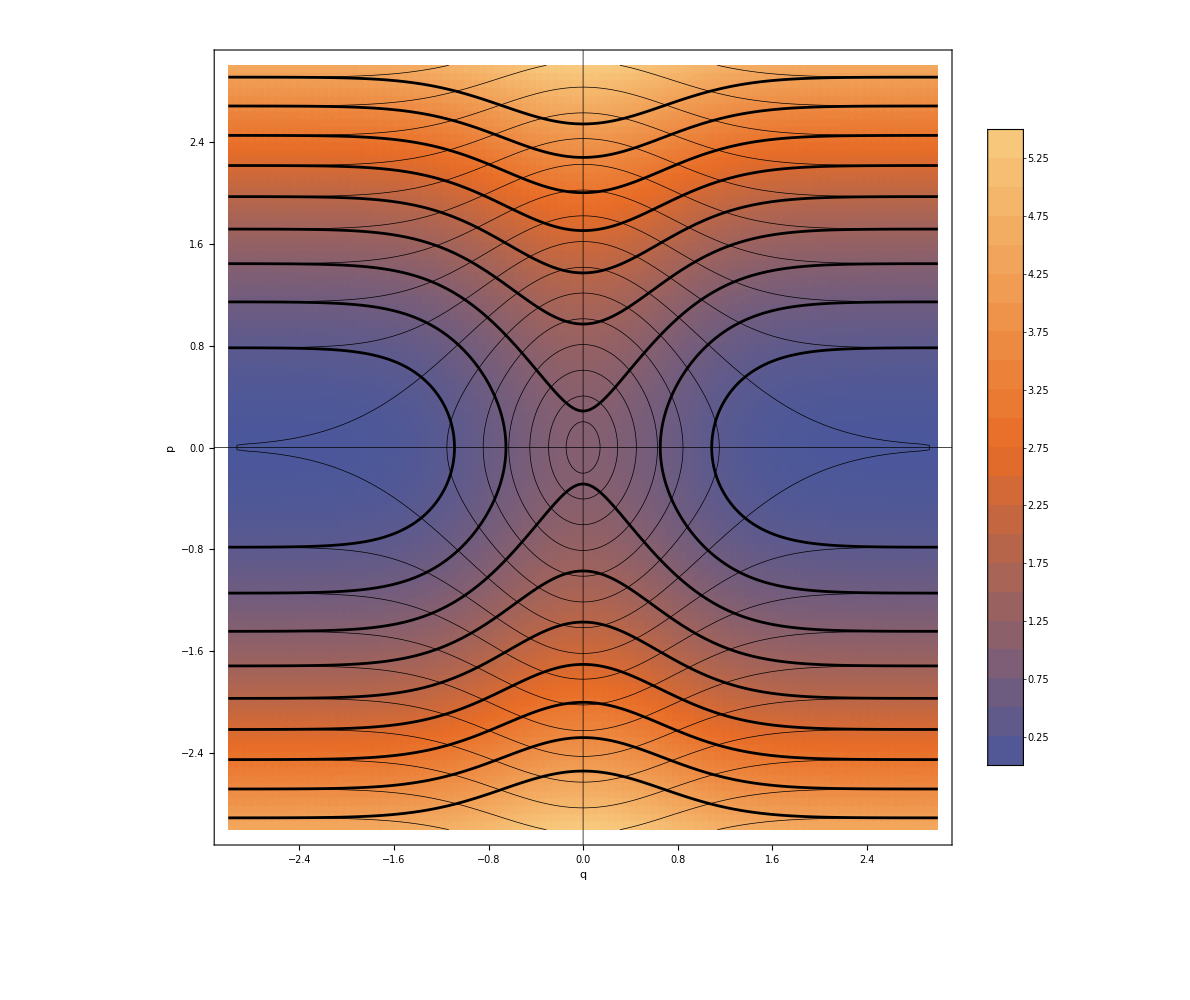

```mathematica
Show[DensityPlot[1/2*y^2+Exp[-x^2],{x,-3,3},{y,-3,3},ImageSize->{1000,1000},FrameLabel->{q,p},Mesh->None,GridLinesStyle->Black,PlotTheme->"Scientific",PlotPoints->100,MaxRecursion->3,
LabelStyle->Directive[Black,FontColor->Black,32,FontFamily->"CMU Serif",Italic],
TicksStyle->Directive[Black,FontColor->Black,12,FontFamily->"CMU Serif",Plain],
FrameStyle->Directive[framestyle,FontColor->Black,FontFamily->"CMU Serif",Plain],PlotRangePadding->0,PlotLegends->BarLegend[{Automatic,{0,5.5}},Table[H,{H,0,5.5,0.25}],LegendLayout->"Column",LegendMarkerSize->{25,940},LabelStyle->Directive[Black,FontColor->Black,30,FontFamily->"CMU Serif"],LegendMargins->{{14,0},{58,0}},Method->{FrameStyle->Directive[Black,Thickness[0.13]],AxesStyle->{Black,Thickness[0.13]}}]],ContourPlot[Evaluate@Table[H@iH==1/2*y^2-Exp[-x^2],{iH,5,20}],{x,-3,3},{y,-3,3},PlotTheme->"Scientific",PlotPoints->100,MaxRecursion->3,ContourStyle->Directive[Black,Thickness[0.0005]]],
ContourPlot[Evaluate@Table[H@iH==1/2*y^2+Exp[-x^2],{iH,5,20}],{x,-3,3},{y,-3,3},PlotTheme->"Scientific",PlotPoints->300,MaxRecursion->3,ContourStyle->Directive[Black,Thickness[0.002]]]] (* Map[Blend[{RGBColor[0.1495428, 0.23820604955094804, 0.706638],RGBColor[0.91, 0.424, 0.1486],RGBColor[0.972554, 0.79695, 0.5]},#]&,Table[(H@iH -H@5)/(H@20-H@5),{iH,5,20}]] *)
```

```mathematica
N[(1/2*y^2+Exp[-x^2])/.{x->0,y->3}]
N[(1/2*y^2+Exp[-x^2])/.{x->3,y->0}]
```

5.5

0.00012341